```mathematica
SetDirectory["L:/moose/project2/trunk/elk"]
```

L:\moose\project2\trunk\elk

```mathematica
ClearAll[f,u,uprime,zstar,theta,tau,z];
kn=0;
ks = 1;
deltaK=ks-kn;
thn=0;
ths=1;
deltatheta=ths-thn;
cc = 1.5;
las=2;
rr=0.0; (* note zero rainfall *)
rrstar=(rr-kn)/deltaK;
m=4cc(cc-1);
rho=rrstar/m;
ts=las*deltatheta/deltaK;

th0 = 1;
aa0 = 1 - cc deltatheta/(cc deltatheta - th0 + thn);

f[x_] := Exp[x^2]Erfc[x];

u[zeta_,tau_]:=Erfc[zeta/Sqrt[tau]] + (1/2)Exp[-zeta^2/tau](f[-(1/2)aa0 Sqrt[tau] - zeta/Sqrt[tau]] - f[-(1/2)aa0 Sqrt[tau] + zeta/Sqrt[tau]]);
uprime[zeta_,tau_]:=Evaluate[D[u[z,tau],z]/.z->zeta];

zstar[zeta_,tau_]:=(1/cc)*(rho(1+rho) tau + (2 rho+1) zeta - Log[u[zeta,tau]]);
theta[zeta_,tau_]:=cc*(1 - 1/(2rho+1-uprime[zeta,tau]/u[zeta,tau]));

tau[t_] := m*t/ts;
z[zeta_,tau_] := las*zstar[zeta,tau];
```

```mathematica
ans={theta[#,tau[100]],z[#,tau[100]]}&/@Range[0,2000,1];
```

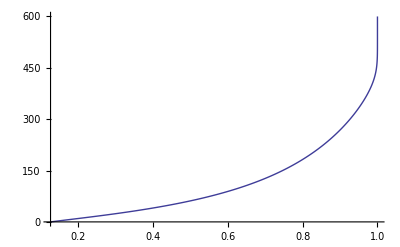

```mathematica
ListLinePlot[ans,PlotRange->All]
```

```mathematica
Export["doc/richards/tests/data/wli01_analytic_100.csv",ans,"Table"]
```

doc/richards/tests/data/wli01_analytic_100.csv